```mathematica
oldboat = ImplicitRegion[x^2/2<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y,z}]
```

ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2&&-5<z<5,{x,y,z}]

```mathematica
boat = ImplicitRegion[x^2/2^2+y^2/2^2 +z^2/4^2<1 ,{ {x,-2,2},{y,-2,0},{z,-4,4}}];
```

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"y","x","z"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.5]]],
ListPointPlot3D[{{0,-0.5008819219921405,0}}, PlotStyle->Directive[Cyan,Opacity[1]]]]
```

-Graphics3D-

```mathematica
boatmass[boatregion_, density_] :=
 mass = N[(Volume[boatregion]*300)+5000,7]
boatcom[boatregion_, density_] := 
com = N[ 1/boatmass[boatregion, density]*NIntegrate[300*{x,y,z}, {x,y,z}∈boatregion],7]
moment[hullshape_,mass_,com_,density_, theta_]:= Module[{},
rads = theta * (Pi/180);
water = ImplicitRegion[If[rads<Pi / 2,y<Tan[rads ]*x+d,y>Tan[rads]*x+d],{{x,-2,2},{y,-2,2}, {z,-5,5}}];
under = RegionIntersection[hullshape, water];
disp = Integrate[1000, {x,y,z}∈under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft}];
buoyancy = mass*98/10*{-Sin[rads],Cos[rads],0};
torque =Cross[cob-com, buoyancy][[3]];
torque]

moment[oldboat,boatmass[oldboat, 300.],boatcom[oldboat,300.],300.,30.]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

91518.2

```mathematica
boatmass[boat,300.]
```

15053.1

```mathematica
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,75.]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-11507.8

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

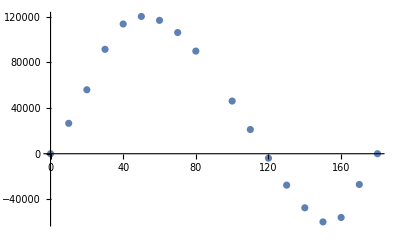

```mathematica
ListPlot[ParallelTable[{theta,moment[oldboat,boatmass[oldboat, 300],boatcom[oldboat,300],300,theta]},{theta,{0,10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}]]
```

```mathematica
(*data =Parallelize[Table[{theta,moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,theta]},{theta,{0.,10.,20.,30.,40.,50.,60.,70.,80.,100.,110.,120.,130.,140.,150.,160.,170.,180.}}]]*)
```

```mathematica
data = moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,#]& /@ Range[0,30,10]
```

```mathematica
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,10.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,20.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,30.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,40.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,50.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,60.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,70.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,80.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,100.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,120.]
```

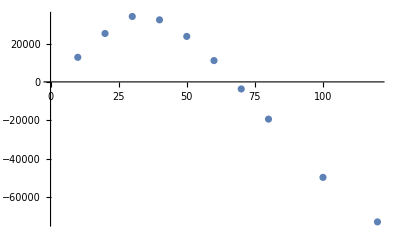

```mathematica
ListPlot[{{10,12830},{20,25272},{30,34154},{40,32391},{50,23743},{60,11126},{70,-3683},{80,-19432},{100,-49838},{120,-73074}}]
```